#### Preparación de la topología

Vamos a definir los parámetros de los círculos.

```mathematica
centroCirculo1={1,0};centroCirculo2={-1,0};centroCirculo3={0,Sqrt[3]};radio1=1.3;radio2=1.6;radio3=1.9;
```

```mathematica
circulo11=Circle[centroCirculo1,radio1];circulo12=Circle[centroCirculo1,radio2];circulo13=Circle[centroCirculo1,radio3];circulo21=Circle[centroCirculo2,radio1];circulo22=Circle[centroCirculo2,radio2];circulo23=Circle[centroCirculo2,radio3];circulo31=Circle[centroCirculo3,radio1];circulo32=Circle[centroCirculo3,radio2];circulo33=Circle[centroCirculo3,radio3];
```

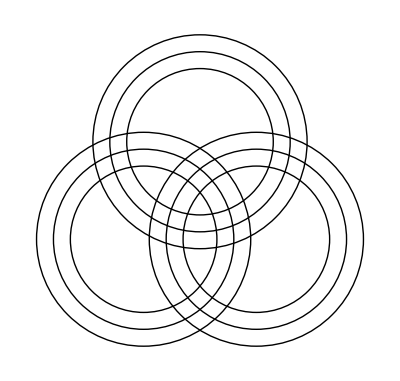

```mathematica
graficaCirculos=Graphics[{circulo11,circulo12,circulo13,circulo21,circulo22,circulo23,circulo31,circulo32,circulo33}]
```

Cada intersección de los círculos genera un punto del cubo. Hay más de una intersección por cada par de círculos (de hecho hay dos cruces por cada par de círculos). Como hay 9 círculos y cada uno se corta con otros 6 círculos 2 veces hay 9x6x2x(1/2)=54 cortes, tantas como caras tiene el cubo. El 1/2 se añade por que cada corte se cuenta 2 veces, una por cada círculo.

Vamos a calcular los cortes de los círculos (sus coordenadas). Tengo que

```mathematica
centroCirculos={centroCirculo1,centroCirculo2,centroCirculo3};
```

```mathematica
radios={radio1,radio2,radio3};
```

```mathematica
listaDePuntos={};Do[(*Bucle i para centro*)
Do[(*Bucle j para cada radio. Con esto ya recorremos los 9 círculos*)
(*Ahora hay que recorrer los otros 6 círuclos que tienen un centro distinto*)
(*Como referencio a los otros centros*)
If[i==1,(*Estamos en el centro 1*)
Do[(*Recorremos para el centro 2*)Do[sol=NSolve[{(x-centroCirculos[[1,1]])^2+(y-centroCirculos[[1,2]])^2==radios[[k]]^2,(x-centroCirculos[[2,1]])^2+(y-centroCirculos[[2,2]])^2==radios[[kk]]^2},{x,y},Reals];punto1={sol[[1,1,2]],sol[[1,2,2]]};punto2={sol[[2,1,2]],sol[[2,2,2]]};listaDePuntos=AppendTo[listaDePuntos,punto1];listaDePuntos=AppendTo[listaDePuntos,punto2];,{kk,1Length[radios]}];
,{k,1,Length[radios]}];
Do[(*Recorremos para el centro 3*)
Do[sol=NSolve[{(x-centroCirculos[[1,1]])^2+(y-centroCirculos[[1,2]])^2==radios[[k]]^2,(x-centroCirculos[[3,1]])^2+(y-centroCirculos[[3,2]])^2==radios[[kk]]^2},{x,y},Reals];punto1={sol[[1,1,2]],sol[[1,2,2]]};punto2={sol[[2,1,2]],sol[[2,2,2]]};listaDePuntos=AppendTo[listaDePuntos,punto1];listaDePuntos=AppendTo[listaDePuntos,punto2];,{kk,1Length[radios]}];
,{k,1,Length[radios]}];,
(*No hacemos nada*)];
If[i==2,(*Estamos en el centro 2*)
Do[(*Recorremos para el centro 1*)Do[sol=NSolve[{(x-centroCirculos[[2,1]])^2+(y-centroCirculos[[2,2]])^2==radios[[k]]^2,(x-centroCirculos[[1,1]])^2+(y-centroCirculos[[1,2]])^2==radios[[kk]]^2},{x,y},Reals];punto1={sol[[1,1,2]],sol[[1,2,2]]};punto2={sol[[2,1,2]],sol[[2,2,2]]};listaDePuntos=AppendTo[listaDePuntos,punto1];listaDePuntos=AppendTo[listaDePuntos,punto2];,{kk,1Length[radios]}];
,{k,1,Length[radios]}];
Do[(*Recorremos para el centro 3*)
Do[sol=NSolve[{(x-centroCirculos[[2,1]])^2+(y-centroCirculos[[2,2]])^2==radios[[k]]^2,(x-centroCirculos[[3,1]])^2+(y-centroCirculos[[3,2]])^2==radios[[kk]]^2},{x,y},Reals];punto1={sol[[1,1,2]],sol[[1,2,2]]};punto2={sol[[2,1,2]],sol[[2,2,2]]};listaDePuntos=AppendTo[listaDePuntos,punto1];listaDePuntos=AppendTo[listaDePuntos,punto2];,{kk,1Length[radios]}];
,{k,1,Length[radios]}];,
(*No hacemos nada*)];
If[i==3,(*Estamos en el centro 3*)
Do[(*Recorremos para el centro 1*)Do[sol=NSolve[{(x-centroCirculos[[3,1]])^2+(y-centroCirculos[[3,2]])^2==radios[[k]]^2,(x-centroCirculos[[1,1]])^2+(y-centroCirculos[[1,2]])^2==radios[[kk]]^2},{x,y},Reals];punto1={sol[[1,1,2]],sol[[1,2,2]]};punto2={sol[[2,1,2]],sol[[2,2,2]]};listaDePuntos=AppendTo[listaDePuntos,punto1];listaDePuntos=AppendTo[listaDePuntos,punto2];,{kk,1Length[radios]}];
,{k,1,Length[radios]}];
Do[(*Recorremos para el centro 2*)
Do[sol=NSolve[{(x-centroCirculos[[3,1]])^2+(y-centroCirculos[[3,2]])^2==radios[[k]]^2,(x-centroCirculos[[2,1]])^2+(y-centroCirculos[[2,2]])^2==radios[[kk]]^2},{x,y},Reals];punto1={sol[[1,1,2]],sol[[1,2,2]]};punto2={sol[[2,1,2]],sol[[2,2,2]]};listaDePuntos=AppendTo[listaDePuntos,punto1];listaDePuntos=AppendTo[listaDePuntos,punto2];,{kk,1Length[radios]}];
,{k,1,Length[radios]}];,
(*No hacemos nada*)];
(*Repetimos lo mismo para los otros 2 círculos*)
,{j,1,Length[radios]}],{i,1,Length[centroCirculos]}]
```

```mathematica
Length[listaDePuntos]
```

324

Obviamente la lista de puntos tiene elementos repetidos.

```mathematica
DuplicateFreeQ[listaDePuntos]
```

False

```mathematica
listaDePuntosSinRep=DeleteDuplicates[listaDePuntos];
```

```mathematica
Length[listaDePuntosSinRep]
```

54

Hay 54 puntos como caras tiene el cubo. Vamos a refinar un poco como pintar las caras y los posibles colores.

```mathematica
listaDePuntosRef={};Do[listaDePuntosRef=AppendTo[listaDePuntosRef,{listaDePuntosSinRep[[i]]}],{i,1,Length[listaDePuntosSinRep]}]
```

```mathematica
pointSize=0.035;colores=Range[Length[listaDePuntosSinRep]];Do[Do[colores[[(i-1)*9+j]]=Switch[i,1,{Orange,PointSize[pointSize]},2,{Red,PointSize[pointSize]},3,{Blue,PointSize[pointSize]},4,{Green,PointSize[pointSize]},5,{Yellow,PointSize[pointSize]},6,{LightGray,PointSize[pointSize]}],{j,1,9}],{i,1,6}];coloresSolución=colores;
```

```mathematica
marker1=Graphics[{{Thickness[0.1],Disk[]},{Black,Thickness[0.15],Circle[]}},ImageSize->14]
```

-Graphics-

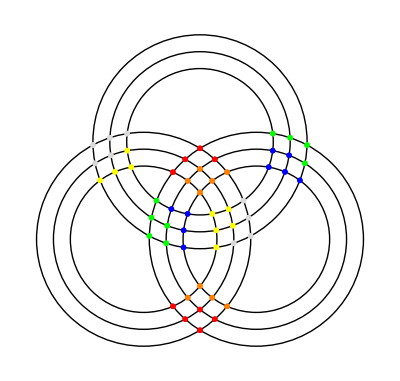

```mathematica
Show[graficaCirculos,ListPlot[listaDePuntosRef,PlotStyle->colores,PlotMarkers->marker1]]
```

Ahora tenemos que ordenar los puntos en un orden que tenga sentido (que tenga las caras enfrentadas con sentido y sea sencillo de operar)

Vamos a calcular los 6 clusters que componen cada cara.

```mathematica
listaDePuntosCluster=FindClusters[listaDePuntosSinRep,6]
```

{{{0.,-0.830662},{0.2175,-1.03812},{0.48,-1.19147},{-0.2175,-1.03812},{0.,-1.249},{0.2625,-1.41989},{-0.48,-1.19147},{-0.2625,-1.41989},{0.,-1.61555}},{{0.,0.830662},{0.2175,1.03812},{0.48,1.19147},{-0.2175,1.03812},{0.,1.249},{0.2625,1.41989},{-0.48,1.19147},{-0.2625,1.41989},{0.,1.61555}},{{1.21937,1.28136},{1.50779,1.19673},{1.77184,1.04607},{1.29029,1.57345},{1.58167,1.49053},{1.86091,1.34864},{1.29184,1.87745},{1.59841,1.8033},{1.89911,1.6738}},{{-0.219375,0.450694},{-0.290289,0.158605},{-0.291843,-0.145402},{-0.507789,0.535326},{-0.581665,0.241526},{-0.598413,-0.0712523},{-0.771843,0.685983},{-0.860913,0.383411},{-0.899107,0.0582507}},{{0.219375,0.450694},{0.290289,0.158605},{0.291843,-0.145402},{0.507789,0.535326},{0.581665,0.241526},{0.598413,-0.0712523},{0.771843,0.685983},{0.860913,0.383411},{0.899107,0.0582507}},{{-1.21937,1.28136},{-1.50779,1.19673},{-1.77184,1.04607},{-1.29029,1.57345},{-1.58167,1.49053},{-1.86091,1.34864},{-1.29184,1.87745},{-1.59841,1.8033},{-1.89911,1.6738}}}

```mathematica
listaFlatten=Flatten[listaDePuntosCluster,1];listaDePuntosClusterRef={};Do[listaDePuntosClusterRef=AppendTo[listaDePuntosClusterRef,{listaFlatten[[i]]}],{i,1,Length[listaFlatten]}]
```

```mathematica
listaDePuntosClusterRef
```

{{{0.,-0.830662}},{{0.2175,-1.03812}},{{0.48,-1.19147}},{{-0.2175,-1.03812}},{{0.,-1.249}},{{0.2625,-1.41989}},{{-0.48,-1.19147}},{{-0.2625,-1.41989}},{{0.,-1.61555}},{{0.,0.830662}},{{0.2175,1.03812}},{{0.48,1.19147}},{{-0.2175,1.03812}},{{0.,1.249}},{{0.2625,1.41989}},{{-0.48,1.19147}},{{-0.2625,1.41989}},{{0.,1.61555}},{{1.21937,1.28136}},{{1.50779,1.19673}},{{1.77184,1.04607}},{{1.29029,1.57345}},{{1.58167,1.49053}},{{1.86091,1.34864}},{{1.29184,1.87745}},{{1.59841,1.8033}},{{1.89911,1.6738}},{{-0.219375,0.450694}},{{-0.290289,0.158605}},{{-0.291843,-0.145402}},{{-0.507789,0.535326}},{{-0.581665,0.241526}},{{-0.598413,-0.0712523}},{{-0.771843,0.685983}},{{-0.860913,0.383411}},{{-0.899107,0.0582507}},{{0.219375,0.450694}},{{0.290289,0.158605}},{{0.291843,-0.145402}},{{0.507789,0.535326}},{{0.581665,0.241526}},{{0.598413,-0.0712523}},{{0.771843,0.685983}},{{0.860913,0.383411}},{{0.899107,0.0582507}},{{-1.21937,1.28136}},{{-1.50779,1.19673}},{{-1.77184,1.04607}},{{-1.29029,1.57345}},{{-1.58167,1.49053}},{{-1.86091,1.34864}},{{-1.29184,1.87745}},{{-1.59841,1.8033}},{{-1.89911,1.6738}}}

```mathematica
<<MaTeX`
```

```mathematica
labelDEH=Rotate[MaTeX["\\leftarrow \\textrm{DEH} ",FontSize->10],30*Pi/180];labelDEA=Rotate[MaTeX["\\textrm{DEA} \\rightarrow",FontSize->10],60*Pi/180];labelDIH=Rotate[MaTeX["\\leftarrow \\textrm{DIH} ",FontSize->10],15*Pi/180];labelDIA=Rotate[MaTeX["\\textrm{DIA} \\rightarrow",FontSize->10],70*Pi/180];labelIEH=Rotate[MaTeX["\\leftarrow \\textrm{IEH} ",FontSize->10],-60*Pi/180];labelIEA=Rotate[MaTeX["\\textrm{IEA} \\rightarrow",FontSize->10],-30*Pi/180];labelIIH=Rotate[MaTeX["\\leftarrow \\textrm{IIH} ",FontSize->10],-70*Pi/180];labelIIA=Rotate[MaTeX["\\textrm{IIA} \\rightarrow",FontSize->10],-15*Pi/180];labelAEH=Rotate[MaTeX["\\textrm{AEH} \\rightarrow",FontSize->10],-30*Pi/180];labelAEA=Rotate[MaTeX["\\leftarrow \\textrm{AEA}",FontSize->10],30*Pi/180];labelAIH=Rotate[MaTeX["\\textrm{AIH} \\rightarrow",FontSize->10],-30*Pi/180];labelAIA=Rotate[MaTeX["\\leftarrow \\textrm{AIA} ",FontSize->10],30*Pi/180];
```

```mathematica
muestraElCubo:=Show[graficaCirculos,ListPlot[listaDePuntosClusterRef,PlotStyle->colores,PlotMarkers->marker1],Epilog->{
Inset[labelDEH,{2.0,-1.8},Automatic,Scaled[.10]],Inset[labelDEA,{2.75,-1.05},Automatic,Scaled[.10]],Inset[labelDIH,{1.2,-1.15},Automatic,Scaled[.10]],Inset[labelDIA,{2.15,-0.25},Automatic,Scaled[.10]],Inset[labelIEH,{-2.75,-1.05},Automatic,Scaled[.10]],Inset[labelIEA,{-2.0,-1.8},Automatic,Scaled[.10]],Inset[labelIIH,{-2.15,-0.25},Automatic,Scaled[.10]],Inset[labelIIA,{-1.2,-1.15},Automatic,Scaled[.10]],
Inset[labelAEH,{1.0,3.5},Automatic,Scaled[.10]],
Inset[labelAEA,{-1.0,3.5},Automatic,Scaled[.10]],Inset[labelAIH,{0.6,2.65},Automatic,Scaled[.10]],
Inset[labelAIA,{-0.6,2.65},Automatic,Scaled[.10]]
}]
```

```mathematica
muestraElCubo
```

-Graphics-

#### Definición del algoritmo de movimiento

Ahora ya tenemos las caras bien diferenciadas y coloreadas adecuadamente (esto se hace eligiendo los colores de la variable colores en el orden adecuado. No es necesario que los colores estén en este orden para hacer el cubo pero suele ser habitual que ciertos colores, rojo y naranja por ejemplo, estén en caras enfrentadas). Los movimientos del cubo lo que hacen es cambiar los colores de la variable colores (su orden en concreto). Hay un total de 18 movimientos (12 si los centros no pueden rotar que se pueden hacer en el cubo). Podemos rotar cada círculo en dos direcciones (9x2=18 ó 6x2=12). Lo que hay que programar una función que actualice la función colores cuando se le de un input.
Para ello hay que hacer un par de cosas:
- Codificar los posibles movimientos de alguna manera (posiblemente con Strings)
- Crear una función que lea el input, reconozco el movimiento y actualice los colores de la variable colores.
- Además, podemos hacer que la función pinte de nuevo las caras de cubo para ver como se ha actualizado.

Para la codificación:
- Como hay 6 círculos que rotar y dos direcciones en las que hacerlo los movimientos se pueden etiquetar como:
“ARRIBA_EXTERIOR_HORARIO” o “DERECHA_INTERIOR_ANTIHORARIO” 
para representar los movimientos. Hay 3 conjuntos de círculos que mover (“ARRIBA”, “DERECHA”, “IZQUIERDA”) con dos círculos cada uno (“EXTERIOR”, “INTERIOR”) y dos sentidos de la rotación (“HORARIO”, “ANTIHORARIO”). Esto se puede simplificar si solo se usa la primera letra de cada caso. Esto es:
“AEH” “DIA”

Para la función. Reconocer el input se puede hacer con u Swicth fácilmente. La cuestión es identificar los movimientos con las posiciones de la función colores. Vamos a ver en que posición se encuentra cada cara del cubo.

```mathematica
listaFlatten=Flatten[listaDePuntosClusterRef,1];listaLabels=Range[Length[listaDePuntosClusterRef]];Do[listaLabels[[i]]={i,listaFlatten[[i,1]],listaFlatten[[i,2]]},{i,1,Length[listaDePuntosClusterRef]}]
```

```mathematica
labels=Text[Style[#[[1]],12],1.1 #[[{2,3}]]]&/@listaLabels;
```

```mathematica
muestraElCuboConLabels:=Show[graficaCirculos,ListPlot[listaDePuntosClusterRef,PlotStyle->colores],Graphics[{Black,labels}]]
```

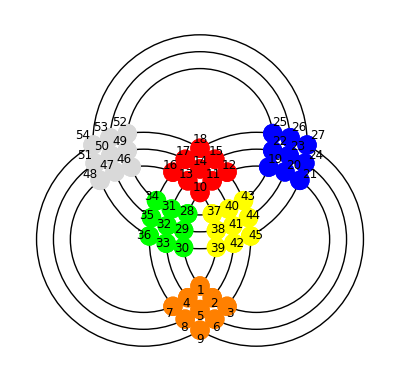

```mathematica
muestraElCuboConLabels
```

Cada movimiento involucra mover 12 elementos de la lista de colores

```mathematica
actualizaColores[swap1_,swap2_,swap3_,swap4_,swap5_,swap6_,swap7_,swap8_,swap9_,swap10_,swap11_,swap12_,swap13_,swap14_,swap15_,swap16_,swap17_,swap18_,swap19_,swap20_]:=Module[{copiaColores},copiaColores=colores;colores[[swap1[[2]]]]=copiaColores[[swap1[[1]]]];colores[[swap2[[2]]]]=copiaColores[[swap2[[1]]]];colores[[swap3[[2]]]]=copiaColores[[swap3[[1]]]];colores[[swap4[[2]]]]=copiaColores[[swap4[[1]]]];colores[[swap5[[2]]]]=copiaColores[[swap5[[1]]]];colores[[swap6[[2]]]]=copiaColores[[swap6[[1]]]];colores[[swap7[[2]]]]=copiaColores[[swap7[[1]]]];colores[[swap8[[2]]]]=copiaColores[[swap8[[1]]]];colores[[swap9[[2]]]]=copiaColores[[swap9[[1]]]];colores[[swap10[[2]]]]=copiaColores[[swap10[[1]]]];colores[[swap11[[2]]]]=copiaColores[[swap11[[1]]]];colores[[swap12[[2]]]]=copiaColores[[swap12[[1]]]];colores[[swap13[[2]]]]=copiaColores[[swap13[[1]]]];colores[[swap14[[2]]]]=copiaColores[[swap14[[1]]]];colores[[swap15[[2]]]]=copiaColores[[swap15[[1]]]];colores[[swap16[[2]]]]=copiaColores[[swap16[[1]]]];colores[[swap17[[2]]]]=copiaColores[[swap17[[1]]]];colores[[swap18[[2]]]]=copiaColores[[swap18[[1]]]];colores[[swap19[[2]]]]=copiaColores[[swap19[[1]]]];colores[[swap20[[2]]]]=copiaColores[[swap20[[1]]]];]
```

```mathematica
movimiento[s_]:=Module[{},Switch[s,
"DIH",(*Movimiento del círculo interior de la derecha en sentido horario*)
actualizaColores[1->28,2->29,3->30,28->12,29->11,30->10,12->21,11->20,10->19,21->1,20->2,19->3,40->44,44->42,42->38,38->40,43->45,45->39,39->37,37->43]
,"DIA",(*Movimiento del círculo interior de la derecha en sentido antihorario*)
actualizaColores[28->1,29->2,30->3,12->28,11->29,10->30,21->12,20->11,19->10,1->21,2->20,3->19,44->40,42->44,38->42,40->38,45->43,39->45,37->39,43->37]
,"DEH",(*Movimiento del círculo exterior de la derecha en sentido horario*)
actualizaColores[7->34,8->35,9->36,34->18,35->17,36->16,18->27,17->26,16->25,27->7,26->8,25->9,46->52,52->54,54->48,48->46,49->53,53->51,51->47,47->49]
,"DEA",(*Movimiento del círculo exterior de la derecha en sentido antihorario*)
actualizaColores[34->7,35->8,36->9,18->34,17->35,16->36,27->18,26->17,25->16,7->27,8->26,9->25,52->46,54->52,48->54,46->48,53->49,51->53,47->51,49->47]
,"IIH",(*Movimiento del círculo interior de la izquierda en sentido horario*)
actualizaColores[1->48,4->47,7->46,48->16,47->13,46->10,16->37,13->38,10->39,37->1,38->4,39->7,34->28,28->30,30->36,36->34,31->29,29->33,33->35,35->31]
,"IIA",(*Movimiento del círculo interior de la izquierda en sentido antihorario*)
actualizaColores[48->1,47->4,46->7,16->48,13->47,10->46,37->16,38->13,39->10,1->37,4->38,7->39,28->34,30->28,36->30,34->36,29->31,33->29,35->33,31->35]
,"IEH",(*Movimiento del círculo exterior de la izquierda en sentido horario*)
actualizaColores[54->18,53->15,52->12,18->43,15->44,12->45,43->3,44->6,45->9,3->54,6->53,9->52,25->19,19->21,21->27,27->25,22->20,20->24,24->26,26->22]
,"IEA",(*Movimiento del círculo exterior de la izquierda en sentido antihorario*)
actualizaColores[18->54,15->53,12->52,43->18,44->15,45->12,3->43,6->44,9->45,54->3,53->6,52->9,19->25,21->19,27->21,25->27,20->22,24->20,26->24,22->26]
,"AIH",(*Movimiento del círculo interior de arriba en sentido horario*)
actualizaColores[25->43,22->40,19->37,43->28,40->31,37->34,28->46,31->49,34->52,46->25,49->22,52->19,17->15,15->11,11->13,13->17,18->12,12->10,10->16,16->18]
,"AIA",(*Movimiento del círculo interior de arriba en sentido antihorario*)
actualizaColores[43->25,40->22,37->19,28->43,31->40,34->37,46->28,49->31,52->34,25->46,22->49,19->52,15->17,11->15,13->11,17->13,12->18,10->12,16->10,18->16]
,"AEH",(*Movimiento del círculo exterior de arriba en sentido horario*)
actualizaColores[48->27,51->24,54->21,27->45,24->42,21->39,45->30,42->33,39->36,30->48,33->51,36->54,1->7,7->9,9->3,3->1,2->4,4->8,8->6,6->2]
,"AEA",(*Movimiento del círculo exterior de arriba en sentido antihorario*)
actualizaColores[27->48,24->51,21->54,45->27,42->24,39->21,30->45,33->42,36->39,48->30,51->33,54->36,7->1,9->7,3->9,1->3,4->2,8->4,6->8,2->6]
];muestraElCubo]
```

Para revolver el cubo vamos hacer aleatoriamente 100 movimientos permitidos en el cubo. Primero vamos a definir una función que nos reinicie el cubo

```mathematica
Clear[reiniciaElCubo]
```

```mathematica
reiniciaElCubo:=Module[{},colores=Range[Length[listaDePuntosSinRep]];Do[Do[colores[[(i-1)*9+j]]=Switch[i,1,{Orange,PointSize[pointSize]},2,{Red,PointSize[pointSize]},3,{Blue,PointSize[pointSize]},4,{Green,PointSize[pointSize]},5,{Yellow,PointSize[pointSize]},6,{LightGray,PointSize[pointSize]}],{j,1,9}],{i,1,6}];muestraElCubo]
```

```mathematica
colores
```

{{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]}}

```mathematica
reiniciaElCubo
```

-Graphics-

```mathematica
colores
```

{{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]}}

Vamos a programar una función que acepte directamente una lista de movimientos. Y luego otra que la llame haciendo n movimientos aleatorios

```mathematica
movimientoLista[listaMovimientos_]:=Module[{l=Length[listaMovimientos]},Do[movimiento[listaMovimientos[[i]]],{i,1,l}];muestraElCubo]
```

```mathematica
movimientoLista[{"IIA","DEH"}]
```

-Graphics-

```mathematica
reiniciaElCubo
```

-Graphics-

```mathematica
listaMovimientosValidos={"DIH","DIA","DEH","DEA","IIH","IIA","IEH","IEA","AIH","AIA","AEH","AEA"}
```

{DIH,DIA,DEH,DEA,IIH,IIA,IEH,IEA,AIH,AIA,AEH,AEA}

```mathematica
revuelveElCubo[nMov_]:=Module[{listaMovimientosHacer,l},listaMovimientosHacer=Range[nMov];l=Length[listaMovimientosValidos];Do[listaMovimientosHacer[[i]]=listaMovimientosValidos[[RandomInteger[{1,l}]]],{i,1,nMov}];movimientoLista[listaMovimientosHacer]]
```

```mathematica
revuelveElCubo[10]
```

-Graphics-

#### Definición de una función que guarda el recorrido hecho hasta ahora

```mathematica
inicializaRecorrido:=Module[{},recorrido={colores};]
```

```mathematica
añadeRecorrido:=Module[{},AppendTo[recorrido,colores];]
```

```mathematica
visualizaRecorrido:=Module[{l=Length[recorrido],plots},plots=Range[l];Do[plots[[i]]=Show[graficaCirculos,ListPlot[listaDePuntosClusterRef,PlotStyle->recorrido[[i]],PlotMarkers->marker1],Epilog->{
Inset[labelDEH,{2.0,-1.8},Automatic,Scaled[.10]],Inset[labelDEA,{2.75,-1.05},Automatic,Scaled[.10]],Inset[labelDIH,{1.2,-1.15},Automatic,Scaled[.10]],Inset[labelDIA,{2.15,-0.25},Automatic,Scaled[.10]],Inset[labelIEH,{-2.75,-1.05},Automatic,Scaled[.10]],Inset[labelIEA,{-2.0,-1.8},Automatic,Scaled[.10]],Inset[labelIIH,{-2.15,-0.25},Automatic,Scaled[.10]],Inset[labelIIA,{-1.2,-1.15},Automatic,Scaled[.10]],
Inset[labelAEH,{1.0,3.5},Automatic,Scaled[.10]],
Inset[labelAEA,{-1.0,3.5},Automatic,Scaled[.10]],Inset[labelAIH,{0.6,2.65},Automatic,Scaled[.10]],
Inset[labelAIA,{-0.6,2.65},Automatic,Scaled[.10]]
}];,{i,1,l}];plots]
```

```mathematica
añadeMovimiento[s_]:=Module[{},listaMov=AppendTo[listaMov,s];]
```

```mathematica
cargaConfiguracion[posicionInicial_,listaMovimientosHechos_]:=Module[{l=Length[listaMovimientosHechos],mov},recorrido={posicionInicial};listaMov={};colores=posicionInicial;Do[mov=listaMovimientosHechos[[i]];movimiento[mov];añadeMovimiento[mov];añadeRecorrido;,{i,1,l}]]
```

#### Prueba

Las funciones que tenemos definidas son:
- reiniciaElCubo 
vuelve al estado original(resuelto)
- revuelveElCubo[n] 
hace n movimientos escogidos aleatoriamente
- movimiento[“XXX”]
hace un movimiento dado como argumento
- movimientoLista[listaMovimientos]
hace una serie de movimientos dados en una lista
- muestraElCubo
enseña la configuración actual del cubo
- muesrtraElCuboConLabels
igual pero con los labels de cada punto

```mathematica
reiniciaElCubo
```

-Graphics-

```mathematica
revuelveElCubo[25]
```

-Graphics-

Guardamos esta posición inicial por si queremos cargarla en otra realización del programa.

Por ejemplo, para la siguiente posición inicial :

```mathematica
posInicial={{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[1, 0.5, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 0, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 0, 1],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{GrayLevel[0.85],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[0, 1, 0],PointSize[0.035]},{RGBColor[1, 1, 0],PointSize[0.035]}};
```

La siguiente combinación de movimientos es solución del cubo :

```mathematica
listaMovGuardada={"DEA","DEA","AEH","AEH","DIH","DIH","DEH","AEA","DEA","IIA","IIA","DIA","DIH","AEA","IEA","IEA","IIA","DIH","IIH","DIA","AEA","DEH","IIH","DEA","IIA","AEH","AEH","IEH","DEA","IEA","DEH","AEH","IEA","DIA","IEH","DIH","AEH","AEH","IIA","AEA","IIH","DEH","IIH","DEA","IIA","AEA","IEH","AEA","IEA","DIA","IEA","DIH","IEH","AEA","AEA","DEH","AEA","DEA","IEH","DEA","IEA","DEH","AEA","AEA","IIH","AEH","IIA","DIH","IIA","DIA","IIH","IIH","AEA","IIA","AEA","IIH","AEA","AEA","IIA","AEA","AEA","AEH","IEA","AEA","IEH","AEA","IEA","AEA","AEA","IEH","AEA","AEA","AEA","IIH","AEH","IEH","AEA","IIA","AEH","IEA","AEA","IEA","AEH","IIA","AEA","IEH","AEH","IIH","AEA","IEA","AEH","IIA","AEA","IEH","AEH","IIH","DIA","AIH","DIH","AIA","DIA","AIH","DIH","AIA","AEA","AEA","DIA","AIH","DIH","AIA","DIA","AIH","DIH","AIA","DIA","AIH","DIH","AIA","DIA","AIH","DIH","AIA","AEA","AEA"};
```

Para jugar de forma dinámica. Los movimientos posibles son: 
“DIH”	(*Movimiento del círculo interior de la derecha en sentido horario*)
”DIA”	(*Movimiento del círculo interior de la derecha en sentido antihorario*)
”DEH”	(*Movimiento del círculo exterior de la derecha en sentido horario*)
”DEA”	(*Movimiento del círculo exterior de la derecha en sentido antihorario*)
”IIH”	(*Movimiento del círculo interior de la izquierda en sentido horario*)
”IIA”  	(*Movimiento del círculo interior de la izquierda en sentido antihorario*)
”IEH”	(*Movimiento del círculo exterior de la izquierda en sentido horario*)
”IEA” 	(*Movimiento del círculo exterior de la izquierda en sentido antihorario*)
”AIH” 	(*Movimiento del círculo interior de arriba en sentido horario*)
”AIA” 	(*Movimiento del círculo interior de arriba en sentido antihorario*)
”AEH” 	(*Movimiento del círculo exterior de arriba en sentido horario*)
”AEA”	(*Movimiento del círculo exterior de arriba en sentido antihorario*)

```mathematica
(*inicializaRecorrido;listaMov={};*)(*Comando para empezar a resolver el cubo desde 0*)
```

```mathematica
cargaConfiguracion[posInicial,listaMovGuardada];(*Comando para cargar la configuracion guardada*)
(*Es recomendable poner ";" en la siguiente linea para que vaya rapido*)
```

Las dos líneas siguientes permiten jugar de form interactiva y guardando el recorrido hecho.

```mathematica
Dynamic[movimiento[mov]];
```

```mathematica
mov="AEA";Pause[0.1];añadeMovimiento[mov];Clear[mov];añadeRecorrido;
```

```mathematica
Dynamic[{Length[recorrido],Length[listaMov]}]
```

#### Saca el gif del recorrido seguido

Una vez hemos acabado vamos a sacar un gif del recorrido seguido.

```mathematica
Length[recorrido]
```

146

```mathematica
plots=visualizaRecorrido;(*Funcion que calcula las imagenes del recorrido seguido*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Usuario\Desktop\Programas de Mathematica\Cubo Rubik

```mathematica
dur=0.5(*Segundos de cada imagen del gif*);duracion=Range[Length[plots]]*0+dur;Export["Cubo_Rubik.gif",plots,"DisplayDurations"-> duracion,ImageSize-> All,ImageResolution-> 200]
```

Cubo_Rubik.gif